```mathematica
(* Efron's dice shall be used as our toy example *)
Efron= {{3,3,3,3,3,3}, {6,6,2,2,2,2},{5,5,5,1,1,1}, {4,4,4,4,0,0}};
(* Convenience function to plot sets of dice graphically*)
DicePlot[d_] := Grid[Prepend[Transpose[d], CharacterRange["A", FromCharacterCode[ToCharacterCode["A"] + Dimensions[d,1][[1]]-1]]], Frame->All]
DicePlot[Efron]
```

A | B | C | D
3 | 6 | 5 | 4
3 | 6 | 5 | 4
3 | 2 | 5 | 4
3 | 2 | 1 | 4
3 | 2 | 1 | 0
3 | 2 | 1 | 0

```mathematica
(* Construct a function which can map from a dice to its beating matrix *)
DiceFaceToDominance[dm_, d_, s_] := Count[dm[[Mod[d, Dimensions[dm][[1]]]+1]], x_ /; x<dm[[d]][[s]]] (* For one face *)
DiceToDominance[dm_] := Table[DiceFaceToDominance[dm, d, s], {d, Dimensions[dm][[1]]}, {s, Dimensions[dm][[2]]}] (* For all faces *)
DicePlot[DiceToDominance[Efron]]
```

A | B | C | D
4 | 6 | 6 | 6
4 | 6 | 6 | 6
4 | 3 | 6 | 6
4 | 3 | 2 | 6
4 | 3 | 2 | 0
4 | 3 | 2 | 0

```mathematica
(* Construct a function which can map a beating matrix back to a dice *)
(*Sanity Test*)
Equal[DominanceToDice[DiceToDominance[Efron]], Efron]
```

DominanceToDice[{{4,4,4,4,4,4},{6,6,3,3,3,3},{6,6,6,2,2,2},{6,6,6,6,0,0}}]=={{3,3,3,3,3,3},{6,6,2,2,2,2},{5,5,5,1,1,1},{4,4,4,4,0,0}}

```mathematica
(* Utility method for overlay printing  top paths *)
PathPlot[path_, s_] := PathPlot[path, Length[path], s]
PathPlot[path_, d_, s_] := 
Module[{tab = Table[Null, {x, d}, {y, s}]},
augPath = Prepend[path, s];
MapIndexed[If[#2[[1]]>1,
tab[[#2-1]][[s-(augPath[[#2-1]]) +1]] = augPath[[#2]];
]&,augPath];
DicePlot[tab]
]
a = PathPlot[{4,3,2,0},4,6]
```

A | B | C | D
4 |  |  | 
 |  |  | 
 | 3 |  | 
 |  | 2 | 
 |  |  | 0
 |  |  |

```mathematica
(*Function to compute dominance of a given number of sides *)
CalculateDominance[s_] :=CalculateDominanceImpl[s-1]
CalculateDominanceImpl[n_] := (6 * n^2 +8 * n + 2 * Mod[n, 2]) / 8


(* Construct a function which can find the quickest-decent top-path for a given number of sides, s and number of dice, dom. *)
GenerateTopPathImpl[d_,dom_]:=Rest[NestWhileList[Max[0,Ceiling[(dom- (d - #1) * d) / #1 ]] &,d, # >0&]]
GenerateTopPath[d_]:=GenerateTopPathImpl[d, CalculateDominance[d]]
GenerateTopPathOLD[s_, dom_] := 
Module[{dice=0, face= s, topPath = {s},lastFace},
While[face > 0,
lastFace = face;
face =Max[Ceiling[(dom - (s - face) * s) / face], 0] ;
If[LessEqual[lastFace, face], Throw[face]]; (* Becoming cyclic, can't be satisfied *)
AppendTo[topPath, face];
];
Delete[topPath, 1] (*Remove virtual entry node *)
]
GenerateTopPathOLD[s_]:=GenerateTopPathOLD[s, CalculateDominance[s]]
ShowTopPath[s_] := PathPlot[GenerateTopPath[s],s] 
ShowTopPath[17]
```

A | B | C | D
4 |  |  | 
 |  |  | 
 | 3 |  | 
 |  | 2 | 
 |  |  | 0
 |  |  |

```mathematica
TopDiv[t_, m_, p_] := Max[0,Min[m,t-m*p]]
Numberer[r_, c_, p_, d_,s_]:= Which[r > p[[c]], TopDiv[d,s,s-r],
						       r == p[[c]], p[[c+1]],
						       r < p[[c]],TopDiv[d - p[[c+1]] - s * (s - p[[c]]) , p[[c+1]], p[[c]]-r-1]]  
CalculateDominanceMatrix[s_] := Module[{toppath,, dice, augPath, r, c},
toppath:=GenerateTopPath[s];
 dice:=Length[toppath];
augPath:=Prepend[toppath, s];
Reverse[Transpose[Table[Numberer[r,c, augPath, CalculateDominance[s],s], {r, s}, {c, dice}]],{2}]
]
PlotDominanceMatrix[s_]:=DicePlot[CalculateDominanceMatrix[s]]
PlotDominanceMatrix[8]
```

A | B | C | D | E | F
6 | 8 | 8 | 8 | 8 | 8
6 | 8 | 8 | 8 | 8 | 8
6 | 5 | 8 | 8 | 8 | 8
6 | 5 | 4 | 8 | 8 | 8
6 | 5 | 4 | 3 | 8 | 8
6 | 5 | 4 | 3 | 2 | 4
6 | 5 | 4 | 3 | 2 | 0
2 | 3 | 4 | 3 | 0 | 0

```mathematica
ConstructDominanceGraphForOneFace[dice_, face_,domMatr_] :=  Union[  Map[{dice, face} -> {1+Mod[dice, Length[domMatr]], #1}&, Length[domMatr[[dice]]]+1-  Range[1,domMatr[[dice]][[face]]]],
Map[{1+Mod[dice, Length[domMatr]], Length[domMatr[[dice]]]+1-#1}  ->  {dice, face}&, Range[domMatr[[dice]][[face]]+1, Length[domMatr[[dice]]]]]]

ConstructDominanceGraph[domMatr_]:=Flatten[MapIndexed[ConstructDominanceGraphForOneFace[#2[[1]], #2[[2]], domMatr] &, domMatr, {2}]]

BuildNonTransitiveDice[dom_] :=Normal[SparseArray[MapIndexed[#1->#2[[1]]&,Reverse[TopologicalSort[Graph[ConstructDominanceGraph[CalculateDominanceMatrix[dom]]]]]]]]

 DicePlot[BuildNonTransitiveDice[6]]
```

A | B | C | D
10 | 23 | 20 | 16
11 | 24 | 21 | 17
12 | 6 | 22 | 18
13 | 7 | 3 | 19
14 | 8 | 4 | 1
15 | 9 | 5 | 2

```mathematica
PrettifyDice[uglyDice_]:=Module[{amberDice, clarifier},
amberDice:=Map[Rest[FoldList[Min,Infinity,#] ]&, uglyDice];
clarifier :=SparseArray[MapIndexed[{#1}->#2[[1]] &,DeleteDuplicates[Sort[Flatten[amberDice]]]]];
Map[clarifier[[#]]-1 &, amberDice, {2}]
]


{DicePlot[PrettifyDice[BuildNonTransitiveDice[9]]],
Graph[ConstructDominanceGraph[CalculateDominanceMatrix[9]]]}
Map[Total[#] &, DiceToDominance[PrettifyDice[BuildNonTransitiveDice[9]]]]
CalculateDominance[9]
```

{A | B | C | D | E | F | G
17 | 23 | 22 | 21 | 20 | 19 | 18
17 | 23 | 22 | 21 | 20 | 19 | 18
17 | 14 | 22 | 21 | 20 | 19 | 18
17 | 14 | 13 | 21 | 20 | 19 | 18
17 | 14 | 13 | 10 | 20 | 19 | 18
17 | 14 | 13 | 8 | 7 | 19 | 18
17 | 14 | 13 | 8 | 7 | 4 | 16
15 | 14 | 11 | 8 | 7 | 2 | 5
6 | 12 | 9 | 8 | 3 | 0 | 1,-Graphics-}

{56,56,56,56,56,56,56}

56

```mathematica
ConstructDominanceGraph[CalculateDominanceMatrix[9]]
```

```mathematica
{{1,1}->{2,3},{1,1}->{2,4},{1,1}->{2,5},{1,1}->{2,6},{1,1}->{2,7},{1,1}->{2,8},{1,1}->{2,9},{2,1}->{1,1},{2,2}->{1,1},{1,2}->{2,3},{1,2}->{2,4},{1,2}->{2,5},{1,2}->{2,6},{1,2}->{2,7},{1,2}->{2,8},{1,2}->{2,9},{2,1}->{1,2},{2,2}->{1,2},{1,3}->{2,3},{1,3}->{2,4},{1,3}->{2,5},{1,3}->{2,6},{1,3}->{2,7},{1,3}->{2,8},{1,3}->{2,9},{2,1}->{1,3},{2,2}->{1,3},{1,4}->{2,3},{1,4}->{2,4},{1,4}->{2,5},{1,4}->{2,6},{1,4}->{2,7},{1,4}->{2,8},{1,4}->{2,9},{2,1}->{1,4},{2,2}->{1,4},{1,5}->{2,3},{1,5}->{2,4},{1,5}->{2,5},{1,5}->{2,6},{1,5}->{2,7},{1,5}->{2,8},{1,5}->{2,9},{2,1}->{1,5},{2,2}->{1,5},{1,6}->{2,3},{1,6}->{2,4},{1,6}->{2,5},{1,6}->{2,6},{1,6}->{2,7},{1,6}->{2,8},{1,6}->{2,9},{2,1}->{1,6},{2,2}->{1,6},{1,7}->{2,3},{1,7}->{2,4},{1,7}->{2,5},{1,7}->{2,6},{1,7}->{2,7},{1,7}->{2,8},{1,7}->{2,9},{2,1}->{1,7},{2,2}->{1,7},{1,8}->{2,3},{1,8}->{2,4},{1,8}->{2,5},{1,8}->{2,6},{1,8}->{2,7},{1,8}->{2,8},{1,8}->{2,9},{2,1}->{1,8},{2,2}->{1,8},{2,1}->{1,9},{2,2}->{1,9},{2,3}->{1,9},{2,4}->{1,9},{2,5}->{1,9},{2,6}->{1,9},{2,7}->{1,9},{2,8}->{1,9},{2,9}->{1,9},{2,1}->{3,1},{2,1}->{3,2},{2,1}->{3,3},{2,1}->{3,4},{2,1}->{3,5},{2,1}->{3,6},{2,1}->{3,7},{2,1}->{3,8},{2,1}->{3,9},{2,2}->{3,1},{2,2}->{3,2},{2,2}->{3,3},{2,2}->{3,4},{2,2}->{3,5},{2,2}->{3,6},{2,2}->{3,7},{2,2}->{3,8},{2,2}->{3,9},{2,3}->{3,4},{2,3}->{3,5},{2,3}->{3,6},{2,3}->{3,7},{2,3}->{3,8},{2,3}->{3,9},{3,1}->{2,3},{3,2}->{2,3},{3,3}->{2,3},{2,4}->{3,4},{2,4}->{3,5},{2,4}->{3,6},{2,4}->{3,7},{2,4}->{3,8},{2,4}->{3,9},{3,1}->{2,4},{3,2}->{2,4},{3,3}->{2,4},{2,5}->{3,4},{2,5}->{3,5},{2,5}->{3,6},{2,5}->{3,7},{2,5}->{3,8},{2,5}->{3,9},{3,1}->{2,5},{3,2}->{2,5},{3,3}->{2,5},{2,6}->{3,4},{2,6}->{3,5},{2,6}->{3,6},{2,6}->{3,7},{2,6}->{3,8},{2,6}->{3,9},{3,1}->{2,6},{3,2}->{2,6},{3,3}->{2,6},{2,7}->{3,4},{2,7}->{3,5},{2,7}->{3,6},{2,7}->{3,7},{2,7}->{3,8},{2,7}->{3,9},{3,1}->{2,7},{3,2}->{2,7},{3,3}->{2,7},{2,8}->{3,4},{2,8}->{3,5},{2,8}->{3,6},{2,8}->{3,7},{2,8}->{3,8},{2,8}->{3,9},{3,1}->{2,8},{3,2}->{2,8},{3,3}->{2,8},{2,9}->{3,8},{2,9}->{3,9},{3,1}->{2,9},{3,2}->{2,9},{3,3}->{2,9},{3,4}->{2,9},{3,5}->{2,9},{3,6}->{2,9},{3,7}->{2,9},{3,1}->{4,1},{3,1}->{4,2},{3,1}->{4,3},{3,1}->{4,4},{3,1}->{4,5},{3,1}->{4,6},{3,1}->{4,7},{3,1}->{4,8},{3,1}->{4,9},{3,2}->{4,1},{3,2}->{4,2},{3,2}->{4,3},{3,2}->{4,4},{3,2}->{4,5},{3,2}->{4,6},{3,2}->{4,7},{3,2}->{4,8},{3,2}->{4,9},{3,3}->{4,1},{3,3}->{4,2},{3,3}->{4,3},{3,3}->{4,4},{3,3}->{4,5},{3,3}->{4,6},{3,3}->{4,7},{3,3}->{4,8},{3,3}->{4,9},{3,4}->{4,5},{3,4}->{4,6},{3,4}->{4,7},{3,4}->{4,8},{3,4}->{4,9},{4,1}->{3,4},{4,2}->{3,4},{4,3}->{3,4},{4,4}->{3,4},{3,5}->{4,5},{3,5}->{4,6},{3,5}->{4,7},{3,5}->{4,8},{3,5}->{4,9},{4,1}->{3,5},{4,2}->{3,5},{4,3}->{3,5},{4,4}->{3,5},{3,6}->{4,5},{3,6}->{4,6},{3,6}->{4,7},{3,6}->{4,8},{3,6}->{4,9},{4,1}->{3,6},{4,2}->{3,6},{4,3}->{3,6},{4,4}->{3,6},{3,7}->{4,5},{3,7}->{4,6},{3,7}->{4,7},{3,7}->{4,8},{3,7}->{4,9},{4,1}->{3,7},{4,2}->{3,7},{4,3}->{3,7},{4,4}->{3,7},{3,8}->{4,5},{3,8}->{4,6},{3,8}->{4,7},{3,8}->{4,8},{3,8}->{4,9},{4,1}->{3,8},{4,2}->{3,8},{4,3}->{3,8},{4,4}->{3,8},{3,9}->{4,6},{3,9}->{4,7},{3,9}->{4,8},{3,9}->{4,9},{4,1}->{3,9},{4,2}->{3,9},{4,3}->{3,9},{4,4}->{3,9},{4,5}->{3,9},{4,1}->{5,1},{4,1}->{5,2},{4,1}->{5,3},{4,1}->{5,4},{4,1}->{5,5},{4,1}->{5,6},{4,1}->{5,7},{4,1}->{5,8},{4,1}->{5,9},{4,2}->{5,1},{4,2}->{5,2},{4,2}->{5,3},{4,2}->{5,4},{4,2}->{5,5},{4,2}->{5,6},{4,2}->{5,7},{4,2}->{5,8},{4,2}->{5,9},{4,3}->{5,1},{4,3}->{5,2},{4,3}->{5,3},{4,3}->{5,4},{4,3}->{5,5},{4,3}->{5,6},{4,3}->{5,7},{4,3}->{5,8},{4,3}->{5,9},{4,4}->{5,1},{4,4}->{5,2},{4,4}->{5,3},{4,4}->{5,4},{4,4}->{5,5},{4,4}->{5,6},{4,4}->{5,7},{4,4}->{5,8},{4,4}->{5,9},{4,5}->{5,6},{4,5}->{5,7},{4,5}->{5,8},{4,5}->{5,9},{5,1}->{4,5},{5,2}->{4,5},{5,3}->{4,5},{5,4}->{4,5},{5,5}->{4,5},{4,6}->{5,6},{4,6}->{5,7},{4,6}->{5,8},{4,6}->{5,9},{5,1}->{4,6},{5,2}->{4,6},{5,3}->{4,6},{5,4}->{4,6},{5,5}->{4,6},{4,7}->{5,6},{4,7}->{5,7},{4,7}->{5,8},{4,7}->{5,9},{5,1}->{4,7},{5,2}->{4,7},{5,3}->{4,7},{5,4}->{4,7},{5,5}->{4,7},{4,8}->{5,6},{4,8}->{5,7},{4,8}->{5,8},{4,8}->{5,9},{5,1}->{4,8},{5,2}->{4,8},{5,3}->{4,8},{5,4}->{4,8},{5,5}->{4,8},{4,9}->{5,6},{4,9}->{5,7},{4,9}->{5,8},{4,9}->{5,9},{5,1}->{4,9},{5,2}->{4,9},{5,3}->{4,9},{5,4}->{4,9},{5,5}->{4,9},{5,1}->{6,1},{5,1}->{6,2},{5,1}->{6,3},{5,1}->{6,4},{5,1}->{6,5},{5,1}->{6,6},{5,1}->{6,7},{5,1}->{6,8},{5,1}->{6,9},{5,2}->{6,1},{5,2}->{6,2},{5,2}->{6,3},{5,2}->{6,4},{5,2}->{6,5},{5,2}->{6,6},{5,2}->{6,7},{5,2}->{6,8},{5,2}->{6,9},{5,3}->{6,1},{5,3}->{6,2},{5,3}->{6,3},{5,3}->{6,4},{5,3}->{6,5},{5,3}->{6,6},{5,3}->{6,7},{5,3}->{6,8},{5,3}->{6,9},{5,4}->{6,1},{5,4}->{6,2},{5,4}->{6,3},{5,4}->{6,4},{5,4}->{6,5},{5,4}->{6,6},{5,4}->{6,7},{5,4}->{6,8},{5,4}->{6,9},{5,5}->{6,1},{5,5}->{6,2},{5,5}->{6,3},{5,5}->{6,4},{5,5}->{6,5},{5,5}->{6,6},{5,5}->{6,7},{5,5}->{6,8},{5,5}->{6,9},{5,6}->{6,7},{5,6}->{6,8},{5,6}->{6,9},{6,1}->{5,6},{6,2}->{5,6},{6,3}->{5,6},{6,4}->{5,6},{6,5}->{5,6},{6,6}->{5,6},{5,7}->{6,7},{5,7}->{6,8},{5,7}->{6,9},{6,1}->{5,7},{6,2}->{5,7},{6,3}->{5,7},{6,4}->{5,7},{6,5}->{5,7},{6,6}->{5,7},{5,8}->{6,7},{5,8}->{6,8},{5,8}->{6,9},{6,1}->{5,8},{6,2}->{5,8},{6,3}->{5,8},{6,4}->{5,8},{6,5}->{5,8},{6,6}->{5,8},{5,9}->{6,8},{5,9}->{6,9},{6,1}->{5,9},{6,2}->{5,9},{6,3}->{5,9},{6,4}->{5,9},{6,5}->{5,9},{6,6}->{5,9},{6,7}->{5,9},{6,1}->{7,1},{6,1}->{7,2},{6,1}->{7,3},{6,1}->{7,4},{6,1}->{7,5},{6,1}->{7,6},{6,1}->{7,7},{6,1}->{7,8},{6,1}->{7,9},{6,2}->{7,1},{6,2}->{7,2},{6,2}->{7,3},{6,2}->{7,4},{6,2}->{7,5},{6,2}->{7,6},{6,2}->{7,7},{6,2}->{7,8},{6,2}->{7,9},{6,3}->{7,1},{6,3}->{7,2},{6,3}->{7,3},{6,3}->{7,4},{6,3}->{7,5},{6,3}->{7,6},{6,3}->{7,7},{6,3}->{7,8},{6,3}->{7,9},{6,4}->{7,1},{6,4}->{7,2},{6,4}->{7,3},{6,4}->{7,4},{6,4}->{7,5},{6,4}->{7,6},{6,4}->{7,7},{6,4}->{7,8},{6,4}->{7,9},{6,5}->{7,1},{6,5}->{7,2},{6,5}->{7,3},{6,5}->{7,4},{6,5}->{7,5},{6,5}->{7,6},{6,5}->{7,7},{6,5}->{7,8},{6,5}->{7,9},{6,6}->{7,1},{6,6}->{7,2},{6,6}->{7,3},{6,6}->{7,4},{6,6}->{7,5},{6,6}->{7,6},{6,6}->{7,7},{6,6}->{7,8},{6,6}->{7,9},{6,7}->{7,9},{7,1}->{6,7},{7,2}->{6,7},{7,3}->{6,7},{7,4}->{6,7},{7,5}->{6,7},{7,6}->{6,7},{7,7}->{6,7},{7,8}->{6,7},{6,8}->{7,9},{7,1}->{6,8},{7,2}->{6,8},{7,3}->{6,8},{7,4}->{6,8},{7,5}->{6,8},{7,6}->{6,8},{7,7}->{6,8},{7,8}->{6,8},{7,1}->{6,9},{7,2}->{6,9},{7,3}->{6,9},{7,4}->{6,9},{7,5}->{6,9},{7,6}->{6,9},{7,7}->{6,9},{7,8}->{6,9},{7,9}->{6,9},{7,1}->{1,1},{7,1}->{1,2},{7,1}->{1,3},{7,1}->{1,4},{7,1}->{1,5},{7,1}->{1,6},{7,1}->{1,7},{7,1}->{1,8},{7,1}->{1,9},{7,2}->{1,1},{7,2}->{1,2},{7,2}->{1,3},{7,2}->{1,4},{7,2}->{1,5},{7,2}->{1,6},{7,2}->{1,7},{7,2}->{1,8},{7,2}->{1,9},{7,3}->{1,1},{7,3}->{1,2},{7,3}->{1,3},{7,3}->{1,4},{7,3}->{1,5},{7,3}->{1,6},{7,3}->{1,7},{7,3}->{1,8},{7,3}->{1,9},{7,4}->{1,1},{7,4}->{1,2},{7,4}->{1,3},{7,4}->{1,4},{7,4}->{1,5},{7,4}->{1,6},{7,4}->{1,7},{7,4}->{1,8},{7,4}->{1,9},{7,5}->{1,1},{7,5}->{1,2},{7,5}->{1,3},{7,5}->{1,4},{7,5}->{1,5},{7,5}->{1,6},{7,5}->{1,7},{7,5}->{1,8},{7,5}->{1,9},{7,6}->{1,1},{7,6}->{1,2},{7,6}->{1,3},{7,6}->{1,4},{7,6}->{1,5},{7,6}->{1,6},{7,6}->{1,7},{7,6}->{1,8},{7,6}->{1,9},{1,1}->{7,7},{1,2}->{7,7},{1,3}->{7,7},{1,4}->{7,7},{1,5}->{7,7},{1,6}->{7,7},{1,7}->{7,7},{7,7}->{1,8},{7,7}->{1,9},{1,1}->{7,8},{1,2}->{7,8},{1,3}->{7,8},{1,4}->{7,8},{1,5}->{7,8},{1,6}->{7,8},{1,7}->{7,8},{1,8}->{7,8},{1,9}->{7,8},{1,1}->{7,9},{1,2}->{7,9},{1,3}->{7,9},{1,4}->{7,9},{1,5}->{7,9},{1,6}->{7,9},{1,7}->{7,9},{1,8}->{7,9},{1,9}->{7,9}}
Graph[%]
```

{{1,1}->{2,3},{1,1}->{2,4},{1,1}->{2,5},{1,1}->{2,6},{1,1}->{2,7},{1,1}->{2,8},{1,1}->{2,9},{2,1}->{1,1},{2,2}->{1,1},{1,2}->{2,3},{1,2}->{2,4},{1,2}->{2,5},{1,2}->{2,6},{1,2}->{2,7},{1,2}->{2,8},{1,2}->{2,9},{2,1}->{1,2},{2,2}->{1,2},{1,3}->{2,3},{1,3}->{2,4},{1,3}->{2,5},{1,3}->{2,6},{1,3}->{2,7},{1,3}->{2,8},{1,3}->{2,9},{2,1}->{1,3},{2,2}->{1,3},{1,4}->{2,3},{1,4}->{2,4},{1,4}->{2,5},{1,4}->{2,6},{1,4}->{2,7},{1,4}->{2,8},{1,4}->{2,9},{2,1}->{1,4},{2,2}->{1,4},{1,5}->{2,3},{1,5}->{2,4},{1,5}->{2,5},{1,5}->{2,6},{1,5}->{2,7},{1,5}->{2,8},{1,5}->{2,9},{2,1}->{1,5},{2,2}->{1,5},{1,6}->{2,3},{1,6}->{2,4},{1,6}->{2,5},{1,6}->{2,6},{1,6}->{2,7},{1,6}->{2,8},{1,6}->{2,9},{2,1}->{1,6},{2,2}->{1,6},{1,7}->{2,3},{1,7}->{2,4},{1,7}->{2,5},{1,7}->{2,6},{1,7}->{2,7},{1,7}->{2,8},{1,7}->{2,9},{2,1}->{1,7},{2,2}->{1,7},{1,8}->{2,3},{1,8}->{2,4},{1,8}->{2,5},{1,8}->{2,6},{1,8}->{2,7},{1,8}->{2,8},{1,8}->{2,9},{2,1}->{1,8},{2,2}->{1,8},{2,1}->{1,9},{2,2}->{1,9},{2,3}->{1,9},{2,4}->{1,9},{2,5}->{1,9},{2,6}->{1,9},{2,7}->{1,9},{2,8}->{1,9},{2,9}->{1,9},{2,1}->{3,1},{2,1}->{3,2},{2,1}->{3,3},{2,1}->{3,4},{2,1}->{3,5},{2,1}->{3,6},{2,1}->{3,7},{2,1}->{3,8},{2,1}->{3,9},{2,2}->{3,1},{2,2}->{3,2},{2,2}->{3,3},{2,2}->{3,4},{2,2}->{3,5},{2,2}->{3,6},{2,2}->{3,7},{2,2}->{3,8},{2,2}->{3,9},{2,3}->{3,4},{2,3}->{3,5},{2,3}->{3,6},{2,3}->{3,7},{2,3}->{3,8},{2,3}->{3,9},{3,1}->{2,3},{3,2}->{2,3},{3,3}->{2,3},{2,4}->{3,4},{2,4}->{3,5},{2,4}->{3,6},{2,4}->{3,7},{2,4}->{3,8},{2,4}->{3,9},{3,1}->{2,4},{3,2}->{2,4},{3,3}->{2,4},{2,5}->{3,4},{2,5}->{3,5},{2,5}->{3,6},{2,5}->{3,7},{2,5}->{3,8},{2,5}->{3,9},{3,1}->{2,5},{3,2}->{2,5},{3,3}->{2,5},{2,6}->{3,4},{2,6}->{3,5},{2,6}->{3,6},{2,6}->{3,7},{2,6}->{3,8},{2,6}->{3,9},{3,1}->{2,6},{3,2}->{2,6},{3,3}->{2,6},{2,7}->{3,4},{2,7}->{3,5},{2,7}->{3,6},{2,7}->{3,7},{2,7}->{3,8},{2,7}->{3,9},{3,1}->{2,7},{3,2}->{2,7},{3,3}->{2,7},{2,8}->{3,4},{2,8}->{3,5},{2,8}->{3,6},{2,8}->{3,7},{2,8}->{3,8},{2,8}->{3,9},{3,1}->{2,8},{3,2}->{2,8},{3,3}->{2,8},{2,9}->{3,8},{2,9}->{3,9},{3,1}->{2,9},{3,2}->{2,9},{3,3}->{2,9},{3,4}->{2,9},{3,5}->{2,9},{3,6}->{2,9},{3,7}->{2,9},{3,1}->{4,1},{3,1}->{4,2},{3,1}->{4,3},{3,1}->{4,4},{3,1}->{4,5},{3,1}->{4,6},{3,1}->{4,7},{3,1}->{4,8},{3,1}->{4,9},{3,2}->{4,1},{3,2}->{4,2},{3,2}->{4,3},{3,2}->{4,4},{3,2}->{4,5},{3,2}->{4,6},{3,2}->{4,7},{3,2}->{4,8},{3,2}->{4,9},{3,3}->{4,1},{3,3}->{4,2},{3,3}->{4,3},{3,3}->{4,4},{3,3}->{4,5},{3,3}->{4,6},{3,3}->{4,7},{3,3}->{4,8},{3,3}->{4,9},{3,4}->{4,5},{3,4}->{4,6},{3,4}->{4,7},{3,4}->{4,8},{3,4}->{4,9},{4,1}->{3,4},{4,2}->{3,4},{4,3}->{3,4},{4,4}->{3,4},{3,5}->{4,5},{3,5}->{4,6},{3,5}->{4,7},{3,5}->{4,8},{3,5}->{4,9},{4,1}->{3,5},{4,2}->{3,5},{4,3}->{3,5},{4,4}->{3,5},{3,6}->{4,5},{3,6}->{4,6},{3,6}->{4,7},{3,6}->{4,8},{3,6}->{4,9},{4,1}->{3,6},{4,2}->{3,6},{4,3}->{3,6},{4,4}->{3,6},{3,7}->{4,5},{3,7}->{4,6},{3,7}->{4,7},{3,7}->{4,8},{3,7}->{4,9},{4,1}->{3,7},{4,2}->{3,7},{4,3}->{3,7},{4,4}->{3,7},{3,8}->{4,5},{3,8}->{4,6},{3,8}->{4,7},{3,8}->{4,8},{3,8}->{4,9},{4,1}->{3,8},{4,2}->{3,8},{4,3}->{3,8},{4,4}->{3,8},{3,9}->{4,6},{3,9}->{4,7},{3,9}->{4,8},{3,9}->{4,9},{4,1}->{3,9},{4,2}->{3,9},{4,3}->{3,9},{4,4}->{3,9},{4,5}->{3,9},{4,1}->{5,1},{4,1}->{5,2},{4,1}->{5,3},{4,1}->{5,4},{4,1}->{5,5},{4,1}->{5,6},{4,1}->{5,7},{4,1}->{5,8},{4,1}->{5,9},{4,2}->{5,1},{4,2}->{5,2},{4,2}->{5,3},{4,2}->{5,4},{4,2}->{5,5},{4,2}->{5,6},{4,2}->{5,7},{4,2}->{5,8},{4,2}->{5,9},{4,3}->{5,1},{4,3}->{5,2},{4,3}->{5,3},{4,3}->{5,4},{4,3}->{5,5},{4,3}->{5,6},{4,3}->{5,7},{4,3}->{5,8},{4,3}->{5,9},{4,4}->{5,1},{4,4}->{5,2},{4,4}->{5,3},{4,4}->{5,4},{4,4}->{5,5},{4,4}->{5,6},{4,4}->{5,7},{4,4}->{5,8},{4,4}->{5,9},{4,5}->{5,6},{4,5}->{5,7},{4,5}->{5,8},{4,5}->{5,9},{5,1}->{4,5},{5,2}->{4,5},{5,3}->{4,5},{5,4}->{4,5},{5,5}->{4,5},{4,6}->{5,6},{4,6}->{5,7},{4,6}->{5,8},{4,6}->{5,9},{5,1}->{4,6},{5,2}->{4,6},{5,3}->{4,6},{5,4}->{4,6},{5,5}->{4,6},{4,7}->{5,6},{4,7}->{5,7},{4,7}->{5,8},{4,7}->{5,9},{5,1}->{4,7},{5,2}->{4,7},{5,3}->{4,7},{5,4}->{4,7},{5,5}->{4,7},{4,8}->{5,6},{4,8}->{5,7},{4,8}->{5,8},{4,8}->{5,9},{5,1}->{4,8},{5,2}->{4,8},{5,3}->{4,8},{5,4}->{4,8},{5,5}->{4,8},{4,9}->{5,6},{4,9}->{5,7},{4,9}->{5,8},{4,9}->{5,9},{5,1}->{4,9},{5,2}->{4,9},{5,3}->{4,9},{5,4}->{4,9},{5,5}->{4,9},{5,1}->{6,1},{5,1}->{6,2},{5,1}->{6,3},{5,1}->{6,4},{5,1}->{6,5},{5,1}->{6,6},{5,1}->{6,7},{5,1}->{6,8},{5,1}->{6,9},{5,2}->{6,1},{5,2}->{6,2},{5,2}->{6,3},{5,2}->{6,4},{5,2}->{6,5},{5,2}->{6,6},{5,2}->{6,7},{5,2}->{6,8},{5,2}->{6,9},{5,3}->{6,1},{5,3}->{6,2},{5,3}->{6,3},{5,3}->{6,4},{5,3}->{6,5},{5,3}->{6,6},{5,3}->{6,7},{5,3}->{6,8},{5,3}->{6,9},{5,4}->{6,1},{5,4}->{6,2},{5,4}->{6,3},{5,4}->{6,4},{5,4}->{6,5},{5,4}->{6,6},{5,4}->{6,7},{5,4}->{6,8},{5,4}->{6,9},{5,5}->{6,1},{5,5}->{6,2},{5,5}->{6,3},{5,5}->{6,4},{5,5}->{6,5},{5,5}->{6,6},{5,5}->{6,7},{5,5}->{6,8},{5,5}->{6,9},{5,6}->{6,7},{5,6}->{6,8},{5,6}->{6,9},{6,1}->{5,6},{6,2}->{5,6},{6,3}->{5,6},{6,4}->{5,6},{6,5}->{5,6},{6,6}->{5,6},{5,7}->{6,7},{5,7}->{6,8},{5,7}->{6,9},{6,1}->{5,7},{6,2}->{5,7},{6,3}->{5,7},{6,4}->{5,7},{6,5}->{5,7},{6,6}->{5,7},{5,8}->{6,7},{5,8}->{6,8},{5,8}->{6,9},{6,1}->{5,8},{6,2}->{5,8},{6,3}->{5,8},{6,4}->{5,8},{6,5}->{5,8},{6,6}->{5,8},{5,9}->{6,8},{5,9}->{6,9},{6,1}->{5,9},{6,2}->{5,9},{6,3}->{5,9},{6,4}->{5,9},{6,5}->{5,9},{6,6}->{5,9},{6,7}->{5,9},{6,1}->{7,1},{6,1}->{7,2},{6,1}->{7,3},{6,1}->{7,4},{6,1}->{7,5},{6,1}->{7,6},{6,1}->{7,7},{6,1}->{7,8},{6,1}->{7,9},{6,2}->{7,1},{6,2}->{7,2},{6,2}->{7,3},{6,2}->{7,4},{6,2}->{7,5},{6,2}->{7,6},{6,2}->{7,7},{6,2}->{7,8},{6,2}->{7,9},{6,3}->{7,1},{6,3}->{7,2},{6,3}->{7,3},{6,3}->{7,4},{6,3}->{7,5},{6,3}->{7,6},{6,3}->{7,7},{6,3}->{7,8},{6,3}->{7,9},{6,4}->{7,1},{6,4}->{7,2},{6,4}->{7,3},{6,4}->{7,4},{6,4}->{7,5},{6,4}->{7,6},{6,4}->{7,7},{6,4}->{7,8},{6,4}->{7,9},{6,5}->{7,1},{6,5}->{7,2},{6,5}->{7,3},{6,5}->{7,4},{6,5}->{7,5},{6,5}->{7,6},{6,5}->{7,7},{6,5}->{7,8},{6,5}->{7,9},{6,6}->{7,1},{6,6}->{7,2},{6,6}->{7,3},{6,6}->{7,4},{6,6}->{7,5},{6,6}->{7,6},{6,6}->{7,7},{6,6}->{7,8},{6,6}->{7,9},{6,7}->{7,9},{7,1}->{6,7},{7,2}->{6,7},{7,3}->{6,7},{7,4}->{6,7},{7,5}->{6,7},{7,6}->{6,7},{7,7}->{6,7},{7,8}->{6,7},{6,8}->{7,9},{7,1}->{6,8},{7,2}->{6,8},{7,3}->{6,8},{7,4}->{6,8},{7,5}->{6,8},{7,6}->{6,8},{7,7}->{6,8},{7,8}->{6,8},{7,1}->{6,9},{7,2}->{6,9},{7,3}->{6,9},{7,4}->{6,9},{7,5}->{6,9},{7,6}->{6,9},{7,7}->{6,9},{7,8}->{6,9},{7,9}->{6,9},{7,1}->{1,1},{7,1}->{1,2},{7,1}->{1,3},{7,1}->{1,4},{7,1}->{1,5},{7,1}->{1,6},{7,1}->{1,7},{7,1}->{1,8},{7,1}->{1,9},{7,2}->{1,1},{7,2}->{1,2},{7,2}->{1,3},{7,2}->{1,4},{7,2}->{1,5},{7,2}->{1,6},{7,2}->{1,7},{7,2}->{1,8},{7,2}->{1,9},{7,3}->{1,1},{7,3}->{1,2},{7,3}->{1,3},{7,3}->{1,4},{7,3}->{1,5},{7,3}->{1,6},{7,3}->{1,7},{7,3}->{1,8},{7,3}->{1,9},{7,4}->{1,1},{7,4}->{1,2},{7,4}->{1,3},{7,4}->{1,4},{7,4}->{1,5},{7,4}->{1,6},{7,4}->{1,7},{7,4}->{1,8},{7,4}->{1,9},{7,5}->{1,1},{7,5}->{1,2},{7,5}->{1,3},{7,5}->{1,4},{7,5}->{1,5},{7,5}->{1,6},{7,5}->{1,7},{7,5}->{1,8},{7,5}->{1,9},{7,6}->{1,1},{7,6}->{1,2},{7,6}->{1,3},{7,6}->{1,4},{7,6}->{1,5},{7,6}->{1,6},{7,6}->{1,7},{7,6}->{1,8},{7,6}->{1,9},{1,1}->{7,7},{1,2}->{7,7},{1,3}->{7,7},{1,4}->{7,7},{1,5}->{7,7},{1,6}->{7,7},{1,7}->{7,7},{7,7}->{1,8},{7,7}->{1,9},{1,1}->{7,8},{1,2}->{7,8},{1,3}->{7,8},{1,4}->{7,8},{1,5}->{7,8},{1,6}->{7,8},{1,7}->{7,8},{1,8}->{7,8},{1,9}->{7,8},{1,1}->{7,9},{1,2}->{7,9},{1,3}->{7,9},{1,4}->{7,9},{1,5}->{7,9},{1,6}->{7,9},{1,7}->{7,9},{1,8}->{7,9},{1,9}->{7,9}}

-Graphics-

```mathematica
DicePlot[PrettifyDice[BuildNonTransitiveDice[22]]]

ComputeDom
```

A | B | C | D | E | F | G | H | I | J
21 | 31 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 31 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 20 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 20 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 20 | 19 | 28 | 27 | 26 | 25 | 24 | 23 | 22
21 | 20 | 19 | 16 | 27 | 26 | 25 | 24 | 23 | 22
21 | 20 | 19 | 16 | 13 | 26 | 25 | 24 | 23 | 22
21 | 20 | 19 | 16 | 13 | 10 | 25 | 24 | 23 | 22
21 | 20 | 17 | 16 | 11 | 10 | 9 | 24 | 23 | 22
21 | 20 | 17 | 16 | 11 | 10 | 9 | 8 | 23 | 22
21 | 20 | 17 | 16 | 11 | 10 | 9 | 8 | 5 | 22
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 5 | 22
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 5 | 2
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 5 | 2
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 5 | 2
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 5 | 2
21 | 20 | 17 | 14 | 11 | 10 | 9 | 6 | 3 | 0
21 | 18 | 15 | 12 | 11 | 10 | 7 | 4 | 1 | 0

```mathematica
CalculateDominance[x]/x^2
```

(8 (-1+x)+6 (-1+x)^2+2 Mod[-1+x,2])/(8 x^2)

```mathematica
SmartyPants[x_]:=(8 (-1+x)+6 (-1+x)^2+-(1^(x+1))+1)/(8 x^2)
```

```mathematica
SmartyPants[6]
```

```mathematica
95/144
```

```mathematica
SmartyPantss[n_]:=((6*(n-1)^2+8*(n-1)-(-1)^(n-1)+1))/(8n^2)
```

```mathematica
SmartyPantss[x]
```

(1-(-1)^(-1+x)+8 (-1+x)+6 (-1+x)^2)/(8 x^2)

```mathematica
SmartyPantss[6]
```

```mathematica
2/3


Wootle:=SmartyPantss[v]*v^2
```

2/3

```mathematica
Simplify[SmartyPantss[p]]
```

```mathematica
(-1+(-1)^p-4 p+6 p^2)/(8 p^2)
```

```mathematica
TITS[x_]:=(-1+(-1)^x-4 x+6 x^2)/(8 x^2)
```

```mathematica
TITS[6]
```

2/3

```mathematica
p=(-1+(-1)^s-4 s+6 s^2)/(8 s^2)
```

(-1+(-1)^s-4 s+6 s^2)/(8 s^2)

```mathematica
Simplify[p]
```

(-1+(-1)^s-4 s+6 s^2)/(8 s^2)

```mathematica
ApartSquareFree[(-1+(-1)^s-4 s+6 s^2)/(8 s^2),s]
```

3/4+(-1+(-1)^s)/(8 s^2)-1/(2 s)

```mathematica
Expand[(-1+(-1)^s-4 s+6 s^2)/8]
```

-1/8+(-1)^s/8-s/2+(3 s^2)/4

```mathematica
3/4+(-1+(-1)^s)/(8 s^2)-1/(2 s)*s^2
```

3/4+(-1+(-1)^s)/(8 s^2)-s/2

```mathematica
Expand[(-1+(-1)^s-4 s+6 s^2)/(8 s^2)]
```

3/4-1/(8 s^2)+(-1)^s/(8 s^2)-1/(2 s)

```mathematica
Factor[%]
```

(-1+(-1)^s-4 s+6 s^2)/(8 s^2)

```mathematica
Simplify[Wootle
```

1/8 (1-(-1)^(-1+v)+8 (-1+v)+6 (-1+v)^2)

```mathematica
Expand[1/8 (1-(-1)^(-1+v)+8 (-1+v)+6 (-1+v)^2)]
```

-1/8-1/8 (-1)^(-1+v)-v/2+(3 v^2)/4

```mathematica
Simplify[-1/8-1/8 (-1)^(-1+v)-v/2+(3 v^2)/4]
```

1/8 (-1+(-1)^v-4 v+6 v^2)

```mathematica
Expand[1/8 (-1+(-1)^v-4 v+6 v^2)]
```

-1/8+(-1)^v/8-v/2+(3 v^2)/4

```mathematica
s=25
f=6
```

25

6

```mathematica
{25/#1^2 - 6^2 / #1^2, (}&/@{1,2,3, 4, 5,6}
```

{{-11,12},{-11/4,12},{-11/9,12},{-11/16,12},{-11/25,12},{-11/36,12}}

```mathematica
(s-f*(f-1))/#1 & /@ {1,2,3,4,5,6}
```

{-5,-5/2,-5/3,-5/4,-1,-5/6}

```mathematica
{(s-f*(f-#1))/#1, (f^2-s)/#1,#1} & /@ Range[1,6]
```

{{-5,11,1},{1/2,11/2,2},{7/3,11/3,3},{13/4,11/4,4},{19/5,11/5,5},{25/6,11/6,6}}

```mathematica
dom - (s - face) * s) / face
```

```mathematica
f[face_,dom_, s_] :=  (dom - (s - face) * s) / face
```

```mathematica
Series[(D-F (S-x))/x,{x,x,4}]
```

Series::vcnt: Center point x of power series expansion involves the variable x.

Series[(D-F (S-x))/x,{x,x,4}]

```mathematica
f
```

```mathematica
f
```

f

```mathematica
f
```

f

```mathematica
f[6,24,6]
```

4

```mathematica
(d- f* (f- x)) /x
```

(d-f (f-x))/x

```mathematica
f
```

f

```mathematica
g[x_]:=f[x,24,6]
h[x_] := f[x,25,6]
```

```mathematica
g[#]&/@{6,4,3,2}
```

{4,3,2,0}

```mathematica
h[#]&/@{6,4,3,2,1}
```

{25/6,13/4,7/3,1/2,-5}

```mathematica
f[face_,dom_, s_] :=  (CalculateDominance[d] - (d - #1) * d) / #1 
f[face_,dom_, s_] :=  (dom - (s - face) * s) / face 
TopCycler[d_]:=Rest[NestWhileList[Max[0,Ceiling[(CalculateDominance[d] - (d - #1) * d) / #1 ]] &,d, # >0&]]
TopCycler[6]
AssCycler[x_]:=BuildTopPath[x,CalculateDominance[x]]
```

```mathematica
InnerCycler[d_,dom_]:=Rest[NestWhileList[Max[0,Ceiling[(dom- (d - #1) * d) / #1 ]] &,d, # >0&]]
OuterCycler[d_] :=InnerCycler[d, CalculateDominance[d]]
GenerateTopPath[d_,_] :=OuterCycler[d]
GenerateTopPath[d_]:=OuterCycler[d]
PathPlot[GenerateTopPath[6,9]]
```

PathPlot[{4,3,2,0}]

```mathematica
{Max[0,Ceiling[CalculateDominance[6]/6]]}
OuterCycler[6]
```

{Max[0,Ceiling[CalculateDominance[6]/6]]}

```mathematica
{Max[0,Ceiling[CalculateDominance[6]/6]]}
```

```mathematica
Timing[OuterCycler[300000000000]]
```

```mathematica
{{}, {{8.65432500000000004547473508864641189575`6.957833113716669,{225000000000,200000000000,187500000000,180000000000,175000000000,171428571428,168749999999,166666666665,164999999998,163636363634,162499999998,161538461536,160714285712,159999999998,159374999998,158823529410,158333333331,157894736840,157499999998,157142857141,156818181816,156521739128,«1440724»,142951409583,142603860531,142220260263,141794692553,141319871746,140786722192,140183792550,139496424010,138705542742,137785862372,136703130403,135409767620,133837688406,131885918921,129398011674,126117884587,121595485258,114960235141,104280149806,84235062551,32890327155,0}}}, {}}

OuterCycler[6]
```

{8.65433,{225000000000,200000000000,187500000000,180000000000,175000000000,171428571428,168749999999,166666666665,164999999998,163636363634,162499999998,161538461536,160714285712,159999999998,159374999998,158823529410,158333333331,157894736840,157499999998,157142857141,156818181816,156521739128,«1440724»,142951409583,142603860531,142220260263,141794692553,141319871746,140786722192,140183792550,139496424010,138705542742,137785862372,136703130403,135409767620,133837688406,131885918921,129398011674,126117884587,121595485258,114960235141,104280149806,84235062551,32890327155,0}}

{4,3,2,0}

"

```mathematica
x*x == x^2
```

True

```mathematica
DeleteDuplicates[{True,True,True}]
```

{True}

```mathematica
DeleteDuplicates[TopCycler[#] ==GenerateTopPath[#] & /@ Range[1,10000]]
```

$Aborted

```mathematica
AssCycler[10000]
```

{7500,6666,6249,5999,5832,5713,5624,5554,5498,5452,5414,5382,5354,5330,5309,5291,5275,5260,5247,5235,5224,5214,5205,5196,5188,5181,5174,5168,5162,5156,5151,5146,5141,5137,5133,5129,5125,5121,5118,5115,5112,5109,5106,5103,5100,5098,5096,5094,5092,5090,5088,5086,5084,5082,5080,5078,5076,5074,5072,5070,5069,5068,5067,5066,5065,5064,5063,5062,5061,5060,5059,5058,5057,5056,5055,5054,5053,5052,5051,5050,5049,5048,5047,5046,5045,5044,5043,5042,5041,5040,5039,5038,5037,5036,5035,5034,5033,5032,5031,5030,5029,5028,5027,5026,5025,5024,5023,5022,5021,5020,5019,5018,5017,5016,5015,5014,5013,5012,5011,5010,5009,5008,5007,5006,5005,5004,5003,5002,5001,5000,4999,4998,4997,4996,4995,4994,4993,4992,4991,4990,4989,4988,4987,4986,4985,4984,4983,4982,4981,4980,4979,4978,4977,4976,4975,4974,4973,4972,4971,4970,4969,4968,4967,4966,4965,4964,4963,4962,4961,4960,4959,4958,4957,4956,4955,4954,4953,4952,4951,4950,4949,4948,4947,4946,4945,4944,4943,4942,4941,4940,4939,4938,4937,4936,4935,4934,4933,4932,4931,4930,4928,4926,4924,4922,4920,4918,4916,4914,4912,4910,4908,4906,4904,4902,4900,4897,4894,4891,4888,4885,4882,4879,4875,4871,4867,4863,4859,4854,4849,4844,4838,4832,4826,4819,4812,4804,4795,4786,4776,4765,4753,4740,4725,4708,4689,4668,4644,4616,4583,4544,4498,4441,4370,4279,4157,3985,3726,3290,2400,0}

```mathematica
Timing[AssCycler[6000000000]]
```

$Aborted

```mathematica
{45,40,37,35,34,33,32,31,30,29,28,27,26,25,23,20,14,0}
TopCycler[60]
```

{45,40,37,35,34,33,32,31,30,29,28,27,26,25,23,20,14,0}

{45,40,37,35,34,33,32,31,30,29,28,27,26,25,23,20,14,0}

```mathematica
Smasher[x_,d_]:=FoldList[Max[0,Ceiling[f[#1, d, x]]] &, x, Range[1,Length[GenerateTopPath[x,d]]]] (*DOES THIS ALWAYS THWACK OUT WHOLE NUMBERS? *)
Smasher[x_] := Smasher[x, CalculateDominance[x]]
```

```mathematica
Smasher[600]
```

{600,450,400,375,360,350,342,336,332,329,326,324,322,320,318,317,316,315,314,313,312,311,310,309,308,307,306,305,304,303,302,301,300,299,298,297,296,295,294,293,292,291,290,289,288,287,286,285,284,283,281,279,277,275,272,269,265,260,253,244,230,208,166,57,-984}

{450,400,375,360,350,342,336,332,329,326,324,322,320,318,317,316,315,314,313,312,311,310,309,308,307,306,305,304,303,302,301,300,299,298,297,296,295,294,293,292,291,290,289,288,287,286,285,284,283,281,279,277,275,272,269,265,260,253,244,230,208,166,57,0}

```mathematica
Simplify[f[X,CalculateDominance[6],6]]
```

(6 (-2+X))/X

```mathematica
-12/x + x
```

-12/x+x

```mathematica
Ceiling[Smasher[#1]] & /@ Range[6,11]
```

{{6,4,3,2,0},{7,5,4,3,1,-14},{8,6,5,4,3,-1,24},{9,7,5,4,3,0,145,9},{10,7,6,5,4,2,-6},{11,8,7,6,5,3,-3,22}}

```mathematica
Ceiling[Smasher[7]]
```

{7,5,4,3,2,-1}

```mathematica
GenerateTopPath[s,CalculateDominance[s]]
```

```mathematica
GenerateTopPath[7,CalculateDominance[7]]
```

{5,4,3,2,0}

```mathematica
lengths[x_]:=Map[Length[GenerateTopPath[#1, CalculateDominance[#1]]] &, Range[1,x]]
```

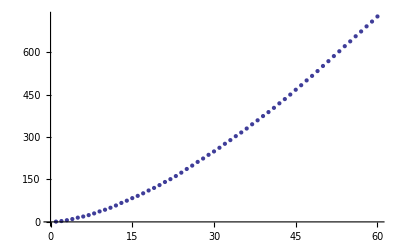

```mathematica
ListPlot[Accumulate[lengths[60]]]
```

```mathematica
c
```

```mathematica
Cumulativ
```

```mathematica
Accumulate[lengths[60]]
```

{1,3,6,10,15,19,24,30,37,43,50,58,67,75,84,92,101,111,120,130,141,151,162,174,187,199,212,224,237,249,262,276,289,303,316,330,345,359,374,388,403,419,434,450,467,483,500,516,533,551,568,586,603,621,638,656,673,691,708,726}

```mathematica
f[face_,dom_, s_] :=  (dom - (s - face) * s) / face
```

```mathematica
magic
```

magic

```mathematica
magic[dice_, dom_, s_] :=RSolve[{a[n] == dom-(s-a[n-1])*s / a[n-1],a[1]==dice},a[n],n ]
```

```mathematica
RSolve[{a[n]==2 a[n-1],a[1]==1},a[n],n]
```

```mathematica
fajic[x_]:=magic[x,CalculateDominance[x],x]
```

```mathematica
f[3,24,6]
```

2

```mathematica
fajic[#] & /@ Range[6,10]
```

{{{a[n]→(3 (-3 (-5/12-(√(7/3))/4)^n+√21 (-5/12-(√(7/3))/4)^n+3 (-5/12+(√(7/3))/4)^n+√21 (-5/12+(√(7/3))/4)^n))/(-9 (-5/12-(√(7/3))/4)^n+2 √21 (-5/12-(√(7/3))/4)^n+9 (-5/12+(√(7/3))/4)^n+2 √21 (-5/12+(√(7/3))/4)^n)}},{{a[n]→(49 (-13 (-20/49-(3 √39)/49)^n+3 √39 (-20/49-(3 √39)/49)^n+13 (-20/49+(3 √39)/49)^n+3 √39 (-20/49+(3 √39)/49)^n))/(-611 (-20/49-(3 √39)/49)^n+99 √39 (-20/49-(3 √39)/49)^n+611 (-20/49+(3 √39)/49)^n+99 √39 (-20/49+(3 √39)/49)^n)}},{{a[n]→(16 (-3 (-13/32-(3 √17)/32)^n+√17 (-13/32-(3 √17)/32)^n+3 (-13/32+(3 √17)/32)^n+√17 (-13/32+(3 √17)/32)^n))/(-45 (-13/32-(3 √17)/32)^n+11 √17 (-13/32-(3 √17)/32)^n+45 (-13/32+(3 √17)/32)^n+11 √17 (-13/32+(3 √17)/32)^n)}},{{a[n]→(81 (-47 (-65/162-(√3901)/162)^n+√3901 (-65/162-(√3901)/162)^n+47 (-65/162+(√3901)/162)^n+√3901 (-65/162+(√3901)/162)^n))/(2 (-1739 (-65/162-(√3901)/162)^n+28 √3901 (-65/162-(√3901)/162)^n+1739 (-65/162+(√3901)/162)^n+28 √3901 (-65/162+(√3901)/162)^n))}},{{a[n]→(10 (-3 (-2/5-(√(3/5))/2)^n+√15 (-2/5-(√(3/5))/2)^n+3 (-2/5+(√(3/5))/2)^n+√15 (-2/5+(√(3/5))/2)^n))/(-27 (-2/5-(√(3/5))/2)^n+7 √15 (-2/5-(√(3/5))/2)^n+27 (-2/5+(√(3/5))/2)^n+7 √15 (-2/5+(√(3/5))/2)^n)}}}

```mathematica
fajic[4]
```

{{a[n]→(8 (-3 (-7/16-(√33)/16)^n+√33 (-7/16-(√33)/16)^n+3 (-7/16+(√33)/16)^n+√33 (-7/16+(√33)/16)^n))/(-27 (-7/16-(√33)/16)^n+5 √33 (-7/16-(√33)/16)^n+27 (-7/16+(√33)/16)^n+5 √33 (-7/16+(√33)/16)^n)}}

```mathematica
Smasher[
```

```mathematica
FindSequenceFunction[Length[GenerateTopPath[#1]]/CalculateDominance[#1] & /@ Range[6,60]]
```

FindSequenceFunction[{1/6,5/33,3/22,1/8,3/35,7/85,4/51,3/40,2/35,9/161,1/23,9/208,5/117,1/29,1/29,11/320,5/176,1/35,1/35,13/456,6/247,1/41,6/287,13/616,1/55,13/705,7/376,13/800,7/425,13/901,7/477,5/336,1/76,15/1121,7/590,3/248,8/651,1/91,8/715,1/88,4/391,17/1633,2/213,17/1776,9/925,17/1925,9/1001,17/2080,1/120,17/2241,9/1162,17/2408,9/1247,17/2581,3/445}]

```mathematica
FindSequenceFunction[CalculateDominance[#1]/Length[GenerateTopPath[#1]] &/@ Range[6,60],n]
```

$Aborted

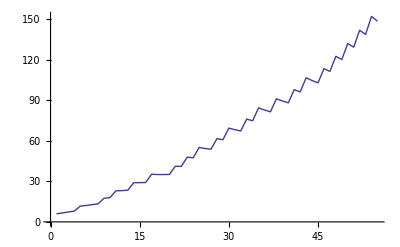
```mathematica
-Graphics-
F[CalculateDominance[#1] & /@ {2}]
```

-Graphics-

```mathematica
FindSequenceFunction[{2,3,4},n]
```

FindSequenceFunction[{2,3,4},n]

```mathematica
Find
```

```mathematica
Click for copyable input
```

```mathematica
FindSequenceFunction[Map[CalculateDominance[#1] &,Range[1,200]],n]
```

1/8 (-1+(-1)^n-4 n+6 n^2)

```mathematica
FindSequenceFunction[Map[CalculateDominance[#1]/Length[GenerateTopPath[#1]] &,Range[1,200]],n]
```

FindSequenceFunction[{0,1,5/3,5/2,16/5,6,33/5,22/3,8,35/3,85/7,51/4,40/3,35/2,161/9,23,208/9,117/5,29,29,320/11,176/5,35,35,456/13,247/6,41,287/6,616/13,55,705/13,376/7,800/13,425/7,901/13,477/7,336/5,76,1121/15,590/7,248/3,651/8,91,715/8,88,391/4,1633/17,213/2,1776/17,925/9,1925/17,1001/9,2080/17,120,2241/17,1162/9,2408/17,1247/9,2581/17,445/3,2760/19,1426/9,155,1520/9,3136/19,1617/10,3333/19,1717/10,3536/21,182,535/3,1926/11,1320/7,185,4181/21,2147/11,4408/21,2262/11,221,2380/11,4880/21,2501/11,5125/21,2625/11,5376/23,2752/11,5633/23,262,5896/23,1005/4,6165/23,3151/12,280,1645/6,6721/23,286,7008/25,3577/12,7301/25,3725/12,304,323,1581/5,310,8216/25,4187/13,8533/25,4347/13,8856/25,4510/13,1837/5,4676/13,9520/27,4845/13,3287/9,5017/13,10208/27,5192/13,10561/27,2685/7,10920/29,793/2,11285/29,5735/14,11656/29,423,12033/29,3056/7,12416/29,6305/14,12805/29,2167/5,13200/29,1340/3,469,6902/15,14008/29,2369/5,14421/29,1463/3,14840/29,7526/15,15265/29,516,15696/31,7957/15,16133/31,8177/15,16576/31,560,17025/31,8626/15,17480/31,1771/3,17941/31,3029/5,18408/31,9322/15,18881/31,1912/3,19360/31,9801/16,19845/31,10045/16,20336/33,2573/4,20833/33,5271/8,7112/11,635,21845/33,11051/17,22360/33,11310/17,7627/11,11572/17,2128/3,11837/17,23941/33,12105/17,4896/7,728,715,12650/17,25576/35,12927/17,26133/35,13207/17,26696/35,13490/17,779,13776/17,5568/7,14065/17,28421/35,14357/17,4144/5,14652/17,29601/35,7475/9},n]

```mathematica
GenerateTopPath[3]
```

{2,1,0}

```mathematica
FindSequenceFunction[Reverse[Smasher[600]]]
```

FindSequenceFunction[{0,57,166,208,230,244,253,260,265,269,272,275,277,279,281,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,320,322,324,326,329,332,336,342,350,360,375,400,450,600}]

```mathematica
OuterCycler[#]==GenerateTopPath[#] & /@ Range[1,50000]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«49876»,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
RemoveDuplicates[%]
```

RemoveDuplicates[Distinct[{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«49880»,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}]]

```mathematica
DeleteDuplicates[%]
```

{True}

```mathematica
Experimental`OptimizeExpression[OuterCycler]
```

Experimental`OptimizedExpression[OuterCycler]

```mathematica
OuterCycler
```

{}

```mathematica
FullSimplify[
```

```mathematica
FullSimplify[Rest[NestWhileList[Max[0,Ceiling[(CalculateDominance[d] - (d - #1) * d) / #1 ]] &,d, # >0&]]]
```

{}

```mathematica
Rooter[xxx_]:=FullSimplify[CalculateDominance[xxx]/xxx^2]
```

```mathematica
CalculateDominance[xx]
```

1/8 (8 (-1+xx)+6 (-1+xx)^2+2 Mod[-1+xx,2])

```mathematica
Timing[CalculateDominance[600000000000000]/600000000000000^2]
```

{0.00005,899999999999999/1200000000000000}

```mathematica
Timing[Rooter[600000000000000]]
```

{0.00009,899999999999999/1200000000000000}

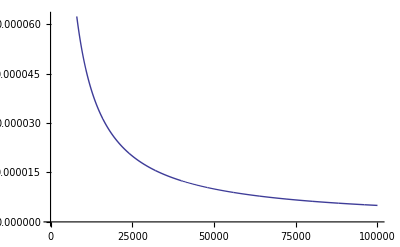

```mathematica
ListLinePlot[0.75-Rooter[#] & /@ Range[1,1000000]]
```

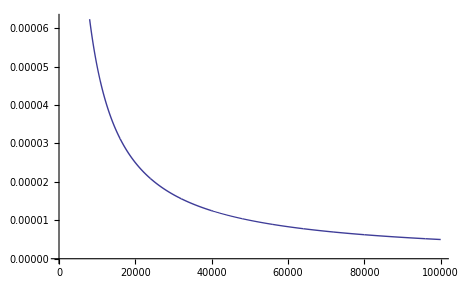

```mathematica
OuterCycler[500]
```

OuterCycler[500]

```mathematica
(*Reminder, use outercycle over GenerateTopCycle, it's awesome and more prettyful *)
(* Next big Thang is a faster numbererere *)
```

```mathematica
GenerateTopPath
```

```mathematica
Definition[GenerateTopPath]
```

GenerateTopPath[s_,dom_]:=Module[{dice=0,face=s,topPath={s},lastFace},While[face>0,lastFace=face;face=Max[Ceiling[(dom-(s-face) s)/face],0];If[lastFace≤face,Throw[face]];AppendTo[topPath,face];];Delete[topPath,1]]
 
GenerateTopPath[s_]:=GenerateTopPath[s,CalculateDominance[s]]